```mathematica
KEYWORD="tongue"
```

tongue

```mathematica
rawTranslations = KeyValueMap[#1->First[#2]&,WordTranslation[KEYWORD, All]];
```

```mathematica
Iconize[rawTranslations]
```

```mathematica
translatedList = Transliterate[Values[rawTranslations]];
translatedList=ToLowerCase[Select[translatedList,StringMatchQ[#,CharacterRange["A","z"]..]&]]
```

{jibha,lengua,azyk,lidah,lingua,jihba,lisan,lidah,she,langue,zunge,zban,ilat,dil,naluka,jibha,hyeo,nakku,lin,lingua,ulimi,awnya,jibha,jezyk,azik,harshe,sezi,nakk,nalige,jibha,jybh,letah,jibha,jibha,dil,limba,dila,tong,dila,ire,jibhro,jibha,nyelv,jila,jabana,demngal,jibha,carrab,glossa,jezik,jazyk,rurimi,zban,linx,ulimi,lilime,lingue,azyk,ezik,tunga,tekrema,til,dila,til,ururimi,ulwimi,dila,lolemu,lezu,llengua,tel,lidah,dil,jezik,alanga,tong,tunge,rurimi,kieli,lswn,jazyk,urulimi,tunge,zyava,leleme,mihi,ena,leleme,lammin,dila,lila,ririmi,lingua,zwng,til,liezuvis,lidah,deene,lango,jezik,arrawo,tel,celhe,lulwimi,lila,jazik,oromeme,ilimu,mele,elelo,lulimi,angajep,me,teod,keel,teanga,lulimi,kewun,qallu,lngejep,lang,oyem,zilim,ziban,menga,edeme,dila,lsien,tyl,laulaufaiva,lengage,kyv,yamena,tunga,lenga,til,arero,setu,jezek,til,uime,tunga,olulimi,lieunga,jilyjil,jihva,ku,singmun,issolash,jijil,razra,jylme,nedep,abas,ichoolaksi,typy,lingua,qallu}

```mathematica
(*translatedList = ToLowerCase[Transliterate[{"sun", WordTranslation[KEYWORD, "Spanish"][[1]], WordTranslation[KEYWORD, "French"][[1]], WordTranslation[KEYWORD, "Portuguese"][[1]], WordTranslation[KEYWORD, "Latin"][[1]], WordTranslation[KEYWORD, "Italian"][[1]], WordTranslation[KEYWORD, "Romanian"][[1]]}]]*)
```

```mathematica
(*originalPopulation = translatedList*)
```

```mathematica
SYLLABLECOUNT=Round[Mean[Length/@(ResourceFunction["WordSyllables"][#]&/@translatedList)]]
net=NetModel["Wolfram English Character-Level Language Model V1","TrainingNet"]
vocabulary=Characters["\t\n !\"#$%&'()*+,-./0123456789:;<=>?@ABCDEFGHIJKLMNOPQRSTUVWXYZ[\\]^_`abcdefghijklmnopqrstuvwxyz{}é"];
net=NetReplacePart[net,"Input"->NetEncoder[{"Characters",{vocabulary,{StartOfString,EndOfString}->97}}]]
results = 
 NetTrain[net, <|"Input" -> translatedList|>, All, LossFunction -> "Loss", 
  MaxTrainingRounds ->300]
trainednet=results["TrainedNet"];
generator=NetReplacePart[NetExtract[trainednet,"predict"],{"Input"->NetEncoder[{"Characters",{vocabulary,EndOfString},"TargetLength"->1}],"Output"->NetDecoder[{"Class",Append[vocabulary,""]}]}]
wordz[]:=With[{obj=NetStateObject[generator]},StringJoin@NestWhileList[obj[Last[#],"RandomSample"]&,{"",""},#=!={""}&,SYLLABLECOUNT,SYLLABLECOUNT+2]];
newAvgWords=Sort@Complement[Table[wordz[],50],translatedList]
```

2

NetGraph[…]

NetGraph[…]

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:1500  rounds:300  time:1.0min  examples/s:771
data | ,,  training examples:158  processed examples:48000  skipped examples:0
method | ,,  ADAMoptimizer  batch size32CPU
round | ,,  loss:8.15×10^-1  error:29.6%
 | 
 | ]

NetChain[<3>]

{alan,arra,awny,celh,hars,jazi,jezi,jibh,jihb,kewu,kue,lele,leng,lida,ling,llen,nalu,qall,razr,ruri,tung,xye,yame,ziba,zili,zyav}

```mathematica
extractor=NetChain[{trainednet,AggregationLayer[Max,1]}]
```

NetChain[<2>]

```mathematica
FeatureSpacePlot[translatedList,FeatureExtractor->extractor,LabelingFunction->Callout]
```

-Graphics-

```mathematica
autocomplete[word_]:=Block[{obj=NetStateObject[NetModel["Wolfram English Character-Level Language Model V1"]]},StringJoin@Most@NestWhileList[obj,word,StringMatchQ[#,LetterCharacter|word]&]]
```

```mathematica
positionedDigrams=Flatten[Table[If[StringLength[word]>=pos+1,{pos,StringTake[word,{pos,pos+1}]},Nothing],{word,translatedList},{pos,StringLength[word]-1}],1];
groupedByPosition=GroupBy[positionedDigrams,First->Last];
countsByPosition=AssociationMap[Counts[groupedByPosition[#]]&,Keys[groupedByPosition]];
topDigramsByPosition=Table[Keys@TakeLargestBy[countsByPosition[pos],Identity,UpTo[5]],{pos,Sort@Keys[countsByPosition]}];
SYLLABLECOUNT=Round[Mean[Length/@(ResourceFunction["WordSyllables"][#]&/@translatedList)]]
```

2

```mathematica
Flatten[topDigramsByPosition]
```

{li,ji,di,le,la,il,ib,in,ez,un,ng,bh,la,zi,li,ha,im,gu,ga,ah,mi,ua,im,ga,me,mi,ep,al,ma,ua,is,fa,sh,ak,ai,ks,iv,si,va}

```mathematica
generateWord[]:=Module[{numSyllables,selectedLists,syllables},numSyllables:=2;
selectedLists=Take[topDigramsByPosition,numSyllables];
syllables=RandomChoice/@selectedLists;
StringJoin[syllables]]
x=DeleteDuplicates[Table[generateWord[],{100}]]
```

{lail,liil,diil,laib,diin,lein,diez,diun,liin,jiun,diib,jiez,lain,liun,laez,jiil,liib,laun,leez,leib,leun,liez,leil,jiin,jiib}

```mathematica
autocomplete/@x
```

{lail,liil,diil,laib,diines,leine,diez,diunda,liin,jiund,diible,jieze,lained,liunciated,laeze,jiil,liible,launched,leezza,leiburn,leun,liez,leiled,jiint,jiib}

```mathematica
words = translatedList;
charSet=Flatten[topDigramsByPosition];


fitnessFunction[candidate_String]:=-Mean[EditDistance[candidate,#]&/@words];


randomString[]:=StringJoin@RandomChoice[Flatten[topDigramsByPosition],RandomInteger[{SYLLABLECOUNT, SYLLABLECOUNT+2}]];

populationSize=100;
generations=500;
mutationRate=0.2;

population=Table[randomString[],{populationSize}]

Do[
fitnesses=fitnessFunction/@population;
bestFitness=Max[fitnesses];
bestCandidate=population[[First@Ordering[fitnesses,-1]]];
parents=TakeLargestBy[Transpose[{population,fitnesses}],Last,Ceiling[populationSize/2]][[All,1]];
crossover[p1_,p2_]:=Module[{len,chars1,chars2},len=Min[StringLength[p1],StringLength[p2]];
chars1=Characters[p1];
chars2=Characters[p2];
StringJoin@Table[RandomChoice[{chars1[[i]],chars2[[i]]}],{i,1,len}]];
mutate[str_]:=StringJoin@Table[If[RandomReal[]<mutationRate,RandomChoice[charSet],c],{c,Characters[str]}];

children=Table[mutate@crossover[RandomChoice[parents],RandomChoice[parents]],{populationSize}];

population=children;

,{gen, 1 , generations}];

bestWord=First@MaximalBy[population,fitnessFunction]
fitnessFunction[bestWord]
```

{ilmi,liun,jiva,ibkslaua,uaziha,ununal,ezak,lagauain,difabh,uaak,aimemela,jiezim,epuaakil,lelimi,laallafa,meaiua,laisuaal,liibng,aileismi,ivks,haivleiv,lemimi,ahbh,ibinak,gaks,haga,miunli,shmiimva,lila,guha,levaalmi,siksaila,isua,simivafa,failinva,hainepdi,valamash,ivibez,shsi,mishla,epepla,haliga,jishng,ngep,meli,guunimib,imfauaga,siahis,meuamail,ismi,hamieziv,uazizime,unakme,ahalmeua,imimme,galiim,sihamimi,epimjiha,shinim,migaib,leimsh,inguua,gafagang,unzi,imuaivgu,imjiks,inal,eplashgu,ilinli,ngngva,gamaga,vaimahil,maua,siaiua,lele,miguli,ivli,ngua,uagush,alimmiez,vala,jiliezak,fami,inma,miua,issiimua,bhal,migaim,inimalil,lega,ezahai,alaiis,shuahaha,miha,ibleun,ziimha,meha,imiviv,diimlama,ilbh}

lila

-298/79

auia

-305/82

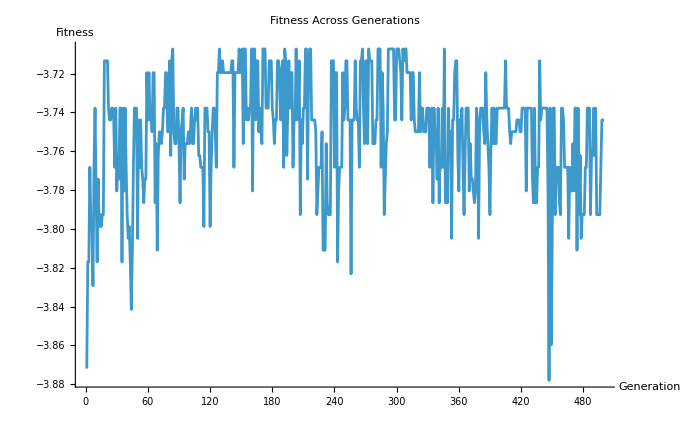

```mathematica
populationSize=100;
generations=500;
mutationRate=0.2;

population=Table[randomString[],{populationSize}];

fitnessValues={}; (* List to store fitness values *)

Do[
  fitnesses=fitnessFunction /@ population;
  bestFitness=Max[fitnesses];
  bestCandidate=population[[First@Ordering[fitnesses,-1]]];
  AppendTo[fitnessValues,bestFitness];
  parents=TakeLargestBy[Transpose[{population,fitnesses}],Last,Ceiling[populationSize/2]][[All,1]];
  crossover[p1_,p2_]:=Module[{len,chars1,chars2},len=Min[StringLength[p1],StringLength[p2]];
    chars1=Characters[p1];
    chars2=Characters[p2];
    StringJoin@Table[RandomChoice[{chars1[[i]],chars2[[i]]}],{i,1,len}]];
  mutate[str_]:=StringJoin@Table[If[RandomReal[]<mutationRate,RandomChoice[charSet],c],{c,Characters[str]}];

  children=Table[mutate@crossover[RandomChoice[parents],RandomChoice[parents]],{populationSize}];

  population=children;

,{gen,1,generations}];

bestWord=First@MaximalBy[population,fitnessFunction];
Print[bestWord];
Print[fitnessFunction[bestWord]];

(* Plot the fitness values *)
ListLinePlot[fitnessValues,AxesLabel->{"Generation","Fitness"},PlotLabel->"Fitness Across Generations"]
```